# The Power Station Problem

## 1. Import the list of coordinates of the power stations and compute its length

```mathematica
L=Import["tridata.dat","Table"]
```

(50 | 50
10 | 100
150 | 20
450 | 350
720 | 80
890 | 105
125 | 650
190 | 780
25 | 920
55 | 100
700 | 150
500 | 500)

```mathematica
s=Length[L]
```

12

## 2. Create the list of triangles

The Table command is used to create a nested list of triangles. They are displayed as a sublist of a sublist (the extra parenthesis);

```mathematica
triangles=Table[{i,j,k},{i,s/3},{j,s/3+1,2s/3},{k,2s/3+1,s}]
```

((1 | 5 | 9
1 | 5 | 10
1 | 5 | 11
1 | 5 | 12) | (1 | 6 | 9
1 | 6 | 10
1 | 6 | 11
1 | 6 | 12) | (1 | 7 | 9
1 | 7 | 10
1 | 7 | 11
1 | 7 | 12) | (1 | 8 | 9
1 | 8 | 10
1 | 8 | 11
1 | 8 | 12)
(2 | 5 | 9
2 | 5 | 10
2 | 5 | 11
2 | 5 | 12) | (2 | 6 | 9
2 | 6 | 10
2 | 6 | 11
2 | 6 | 12) | (2 | 7 | 9
2 | 7 | 10
2 | 7 | 11
2 | 7 | 12) | (2 | 8 | 9
2 | 8 | 10
2 | 8 | 11
2 | 8 | 12)
(3 | 5 | 9
3 | 5 | 10
3 | 5 | 11
3 | 5 | 12) | (3 | 6 | 9
3 | 6 | 10
3 | 6 | 11
3 | 6 | 12) | (3 | 7 | 9
3 | 7 | 10
3 | 7 | 11
3 | 7 | 12) | (3 | 8 | 9
3 | 8 | 10
3 | 8 | 11
3 | 8 | 12)
(4 | 5 | 9
4 | 5 | 10
4 | 5 | 11
4 | 5 | 12) | (4 | 6 | 9
4 | 6 | 10
4 | 6 | 11
4 | 6 | 12) | (4 | 7 | 9
4 | 7 | 10
4 | 7 | 11
4 | 7 | 12) | (4 | 8 | 9
4 | 8 | 10
4 | 8 | 11
4 | 8 | 12))

The Flatten command can be used to flatten out nested lists.

```mathematica
a={{{2,5,3},{4,7,2}}}
```

({2,5,3} | {4,7,2})

```mathematica
Flatten[a,1]
```

(2 | 5 | 3
4 | 7 | 2)

We apply the Flatten command to the nested list of triangles.

```mathematica
Flatten[triangles,2]
```

(1 | 5 | 9
1 | 5 | 10
1 | 5 | 11
1 | 5 | 12
1 | 6 | 9
1 | 6 | 10
1 | 6 | 11
1 | 6 | 12
1 | 7 | 9
1 | 7 | 10
1 | 7 | 11
1 | 7 | 12
1 | 8 | 9
1 | 8 | 10
1 | 8 | 11
1 | 8 | 12
2 | 5 | 9
2 | 5 | 10
2 | 5 | 11
2 | 5 | 12
2 | 6 | 9
2 | 6 | 10
2 | 6 | 11
2 | 6 | 12
2 | 7 | 9
2 | 7 | 10
2 | 7 | 11
2 | 7 | 12
2 | 8 | 9
2 | 8 | 10
2 | 8 | 11
2 | 8 | 12
3 | 5 | 9
3 | 5 | 10
3 | 5 | 11
3 | 5 | 12
3 | 6 | 9
3 | 6 | 10
3 | 6 | 11
3 | 6 | 12
3 | 7 | 9
3 | 7 | 10
3 | 7 | 11
3 | 7 | 12
3 | 8 | 9
3 | 8 | 10
3 | 8 | 11
3 | 8 | 12
4 | 5 | 9
4 | 5 | 10
4 | 5 | 11
4 | 5 | 12
4 | 6 | 9
4 | 6 | 10
4 | 6 | 11
4 | 6 | 12
4 | 7 | 9
4 | 7 | 10
4 | 7 | 11
4 | 7 | 12
4 | 8 | 9
4 | 8 | 10
4 | 8 | 11
4 | 8 | 12)

## 3. Create the list of triangles with corresponding perimeters

```mathematica
perimeters=Table[{i,j,k,N[Sqrt[(L[[i,1]]-L[[j,1]])^2+(L[[i,2]]-L[[j,2]])^2]+Sqrt[(L[[j,1]]-L[[k,1]])^2+(L[[j,2]]-L[[k,2]])^2]+Sqrt[(L[[k,1]]-L[[i,1]])^2+(L[[k,2]]-L[[i,2]])^2],5]},{i,s/3},{j,s/3+1,2s/3},{k,2s/3+1,s}]
```

((1 | 5 | 9 | 2631.3
1 | 5 | 10 | 1386.2
1 | 5 | 11 | 1401.1
1 | 5 | 12 | 1781.2) | (1 | 6 | 9 | 2900.6
1 | 6 | 10 | 1727.1
1 | 6 | 11 | 1694.7
1 | 6 | 12 | 2033.3) | (1 | 7 | 9 | 1763.
1 | 7 | 10 | 1209.4
1 | 7 | 11 | 2024.3
1 | 7 | 12 | 1645.) | (1 | 8 | 9 | 1830.1
1 | 8 | 10 | 1486.8
1 | 8 | 11 | 2211.5
1 | 8 | 12 | 1797.4)
(2 | 5 | 9 | 2620.7
2 | 5 | 10 | 1420.6
2 | 5 | 11 | 1474.9
2 | 5 | 12 | 1816.9) | (2 | 6 | 9 | 2888.6
2 | 6 | 10 | 1760.
2 | 6 | 11 | 1767.1
2 | 6 | 12 | 2067.6) | (2 | 7 | 9 | 1670.
2 | 7 | 10 | 1161.3
2 | 7 | 11 | 2015.7
2 | 7 | 12 | 1598.3) | (2 | 8 | 9 | 1739.9
2 | 8 | 10 | 1441.7
2 | 8 | 11 | 2205.8
2 | 8 | 12 | 1753.7)
(3 | 5 | 9 | 2572.
3 | 5 | 10 | 1362.6
3 | 5 | 11 | 1211.1
3 | 5 | 12 | 1641.3) | (3 | 6 | 9 | 2842.
3 | 6 | 10 | 1704.1
3 | 6 | 11 | 1505.3
3 | 6 | 12 | 1894.) | (3 | 7 | 9 | 1827.1
3 | 7 | 10 | 1309.1
3 | 7 | 11 | 1957.6
3 | 7 | 12 | 1628.4) | (3 | 8 | 9 | 1886.1
3 | 8 | 10 | 1578.5
3 | 8 | 11 | 2136.8
3 | 8 | 12 | 1772.8)
(4 | 5 | 9 | 2183.1
4 | 5 | 10 | 1514.6
4 | 5 | 11 | 774.79
4 | 5 | 12 | 1014.1) | (4 | 6 | 9 | 2403.1
4 | 6 | 10 | 1806.1
4 | 6 | 11 | 1019.
4 | 6 | 12 | 1216.8) | (4 | 7 | 9 | 1441.2
4 | 7 | 10 | 1464.2
4 | 7 | 11 | 1524.4
4 | 7 | 12 | 1004.3) | (4 | 8 | 9 | 1429.9
4 | 8 | 10 | 1663.2
4 | 8 | 11 | 1633.2
4 | 8 | 12 | 1078.3))

The option TableForm displays triangles with their corresponding perimeter.

```mathematica
perimeters//TableForm
```

1 | 5 | 9 | 2631.3
1 | 5 | 10 | 1386.2
1 | 5 | 11 | 1401.1
1 | 5 | 12 | 1781.2 | 1 | 6 | 9 | 2900.6
1 | 6 | 10 | 1727.1
1 | 6 | 11 | 1694.7
1 | 6 | 12 | 2033.3 | 1 | 7 | 9 | 1763.
1 | 7 | 10 | 1209.4
1 | 7 | 11 | 2024.3
1 | 7 | 12 | 1645. | 1 | 8 | 9 | 1830.1
1 | 8 | 10 | 1486.8
1 | 8 | 11 | 2211.5
1 | 8 | 12 | 1797.4
2 | 5 | 9 | 2620.7
2 | 5 | 10 | 1420.6
2 | 5 | 11 | 1474.9
2 | 5 | 12 | 1816.9 | 2 | 6 | 9 | 2888.6
2 | 6 | 10 | 1760.
2 | 6 | 11 | 1767.1
2 | 6 | 12 | 2067.6 | 2 | 7 | 9 | 1670.
2 | 7 | 10 | 1161.3
2 | 7 | 11 | 2015.7
2 | 7 | 12 | 1598.3 | 2 | 8 | 9 | 1739.9
2 | 8 | 10 | 1441.7
2 | 8 | 11 | 2205.8
2 | 8 | 12 | 1753.7
3 | 5 | 9 | 2572.
3 | 5 | 10 | 1362.6
3 | 5 | 11 | 1211.1
3 | 5 | 12 | 1641.3 | 3 | 6 | 9 | 2842.
3 | 6 | 10 | 1704.1
3 | 6 | 11 | 1505.3
3 | 6 | 12 | 1894. | 3 | 7 | 9 | 1827.1
3 | 7 | 10 | 1309.1
3 | 7 | 11 | 1957.6
3 | 7 | 12 | 1628.4 | 3 | 8 | 9 | 1886.1
3 | 8 | 10 | 1578.5
3 | 8 | 11 | 2136.8
3 | 8 | 12 | 1772.8
4 | 5 | 9 | 2183.1
4 | 5 | 10 | 1514.6
4 | 5 | 11 | 774.79
4 | 5 | 12 | 1014.1 | 4 | 6 | 9 | 2403.1
4 | 6 | 10 | 1806.1
4 | 6 | 11 | 1019.
4 | 6 | 12 | 1216.8 | 4 | 7 | 9 | 1441.2
4 | 7 | 10 | 1464.2
4 | 7 | 11 | 1524.4
4 | 7 | 12 | 1004.3 | 4 | 8 | 9 | 1429.9
4 | 8 | 10 | 1663.2
4 | 8 | 11 | 1633.2
4 | 8 | 12 | 1078.3

## 4. Sort by perimeter the list of triangles with corresponding perimeters

The SortBy command with the option Last will sort a list of lists by the last element of each list.

```mathematica
SortBy[a,Last]
```

({2,5,3} | {4,7,2})

The above failed because a is not a list of lists.
Now use Flatten to remove one level of parenthesis.

```mathematica
Flatten[a,1]
```

(2 | 5 | 3
4 | 7 | 2)

```mathematica
SortBy[Flatten[a,1],Last]
```

(4 | 7 | 2
2 | 5 | 3)

Next we remove two levels of parenthesis and sort by perimeter.

```mathematica
p=SortBy[Flatten[perimeters,2],Last]
```

(4 | 5 | 11 | 774.79
4 | 7 | 12 | 1004.3
4 | 5 | 12 | 1014.1
4 | 6 | 11 | 1019.
4 | 8 | 12 | 1078.3
2 | 7 | 10 | 1161.3
1 | 7 | 10 | 1209.4
3 | 5 | 11 | 1211.1
4 | 6 | 12 | 1216.8
3 | 7 | 10 | 1309.1
3 | 5 | 10 | 1362.6
1 | 5 | 10 | 1386.2
1 | 5 | 11 | 1401.1
2 | 5 | 10 | 1420.6
4 | 8 | 9 | 1429.9
4 | 7 | 9 | 1441.2
2 | 8 | 10 | 1441.7
4 | 7 | 10 | 1464.2
2 | 5 | 11 | 1474.9
1 | 8 | 10 | 1486.8
3 | 6 | 11 | 1505.3
4 | 5 | 10 | 1514.6
4 | 7 | 11 | 1524.4
3 | 8 | 10 | 1578.5
2 | 7 | 12 | 1598.3
3 | 7 | 12 | 1628.4
4 | 8 | 11 | 1633.2
3 | 5 | 12 | 1641.3
1 | 7 | 12 | 1645.
4 | 8 | 10 | 1663.2
2 | 7 | 9 | 1670.
1 | 6 | 11 | 1694.7
3 | 6 | 10 | 1704.1
1 | 6 | 10 | 1727.1
2 | 8 | 9 | 1739.9
2 | 8 | 12 | 1753.7
2 | 6 | 10 | 1760.
1 | 7 | 9 | 1763.
2 | 6 | 11 | 1767.1
3 | 8 | 12 | 1772.8
1 | 5 | 12 | 1781.2
1 | 8 | 12 | 1797.4
4 | 6 | 10 | 1806.1
2 | 5 | 12 | 1816.9
3 | 7 | 9 | 1827.1
1 | 8 | 9 | 1830.1
3 | 8 | 9 | 1886.1
3 | 6 | 12 | 1894.
3 | 7 | 11 | 1957.6
2 | 7 | 11 | 2015.7
1 | 7 | 11 | 2024.3
1 | 6 | 12 | 2033.3
2 | 6 | 12 | 2067.6
3 | 8 | 11 | 2136.8
4 | 5 | 9 | 2183.1
2 | 8 | 11 | 2205.8
1 | 8 | 11 | 2211.5
4 | 6 | 9 | 2403.1
3 | 5 | 9 | 2572.
2 | 5 | 9 | 2620.7
1 | 5 | 9 | 2631.3
3 | 6 | 9 | 2842.
2 | 6 | 9 | 2888.6
1 | 6 | 9 | 2900.6)

The triangle with minimal perimeter appears in the list, together with its perimeter, as

```mathematica
p[[1]]
```

{4,5,11,774.79}

## 5. Remove from the list the triangles using power stations in the triangle of minimal perimeter to form the list t and place the minimal triangle with perimeter at the top of the list t

We use the Cases command to select all triangles represented in the list p that do not go through power stations 4, 5, or 11.

```mathematica
t=Cases[p,{a_,b_,c_,d_}/;a≠p[[1,1]]&&b≠p[[1,2]]&&c≠ p[[1,3]]]
```

(2 | 7 | 10 | 1161.3
1 | 7 | 10 | 1209.4
3 | 7 | 10 | 1309.1
2 | 8 | 10 | 1441.7
1 | 8 | 10 | 1486.8
3 | 8 | 10 | 1578.5
2 | 7 | 12 | 1598.3
3 | 7 | 12 | 1628.4
1 | 7 | 12 | 1645.
2 | 7 | 9 | 1670.
3 | 6 | 10 | 1704.1
1 | 6 | 10 | 1727.1
2 | 8 | 9 | 1739.9
2 | 8 | 12 | 1753.7
2 | 6 | 10 | 1760.
1 | 7 | 9 | 1763.
3 | 8 | 12 | 1772.8
1 | 8 | 12 | 1797.4
3 | 7 | 9 | 1827.1
1 | 8 | 9 | 1830.1
3 | 8 | 9 | 1886.1
3 | 6 | 12 | 1894.
1 | 6 | 12 | 2033.3
2 | 6 | 12 | 2067.6
3 | 6 | 9 | 2842.
2 | 6 | 9 | 2888.6
1 | 6 | 9 | 2900.6)

```mathematica
Join[p[[1]],t]
```

{4,5,11,774.79,{2,7,10,1161.3},{1,7,10,1209.4},{3,7,10,1309.1},{2,8,10,1441.7},{1,8,10,1486.8},{3,8,10,1578.5},{2,7,12,1598.3},{3,7,12,1628.4},{1,7,12,1645.},{2,7,9,1670.},{3,6,10,1704.1},{1,6,10,1727.1},{2,8,9,1739.9},{2,8,12,1753.7},{2,6,10,1760.},{1,7,9,1763.},{3,8,12,1772.8},{1,8,12,1797.4},{3,7,9,1827.1},{1,8,9,1830.1},{3,8,9,1886.1},{3,6,12,1894.},{1,6,12,2033.3},{2,6,12,2067.6},{3,6,9,2842.},{2,6,9,2888.6},{1,6,9,2900.6}}

## 6. Repeat step 5 until only the s/3 minimal triangles with perimeters appear in the list p

We will use recursion.

Example: calculate n! using recursion

First define g(0).

```mathematica
g[0]=1
```

1

Then define g(n).

```mathematica
g[n_]:=n*g[n-1]
```

```mathematica
g[4]
```

24

Now recursively apply step 5

```mathematica
f[{}]={}
f[p_List]:=Join[{p[[1]]},f[Cases[p,{a_,b_,c_,d_}/;a≠p[[1,1]]&&b≠p[[1,2]]&&c≠p[[1,3]]]]]
```

{}

```mathematica
V=f[p]
```

(4 | 5 | 11 | 774.79
2 | 7 | 10 | 1161.3
3 | 8 | 12 | 1772.8
1 | 6 | 9 | 2900.6)

```mathematica
length = Length[V]
```

4

## 7. In the same graphic draw the s/3 minimal triangles

Solution:

```mathematica
x = Table[{Line[{{L[[V[[o,1]],1]],L[[V[[o,1]],2]]},{L[[V[[o,2]],1]],L[[V[[o,2]],2]]}}],Line[{{L[[V[[o,2]],1]],L[[V[[o,2]],2]]},{L[[V[[o,3]],1]],L[[V[[o,3]],2]]}}],Line[{{L[[V[[o,3]],1]],L[[V[[o,3]],2]]},{L[[V[[o,1]],1]],L[[V[[o,1]],2]]}}]
},{o,1,length}]
```

(Line[(450 | 350
720 | 80)] | Line[(720 | 80
700 | 150)] | Line[(700 | 150
450 | 350)]
Line[(10 | 100
125 | 650)] | Line[(125 | 650
55 | 100)] | Line[(55 | 100
10 | 100)]
Line[(150 | 20
190 | 780)] | Line[(190 | 780
500 | 500)] | Line[(500 | 500
150 | 20)]
Line[(50 | 50
890 | 105)] | Line[(890 | 105
25 | 920)] | Line[(25 | 920
50 | 50)])

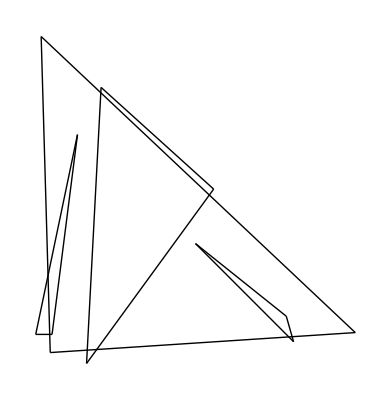

```mathematica
Show[Graphics[x]]
```